## Install Dependencies

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"install_dep.m"}]];
```

```mathematica
InstallMongoDBLink[]
```

Installed MongoDBLink to /Library/Mathematica/Applications

## Run

```mathematica
Exit
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"evaluation.m"}]];
```

```mathematica
$AccuracyInformation
```

{<|Model→BVLC-AlexNet,Framework→Caffe2,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→32,HostName→minsky1,Top1→0.55584,Top5→0.79098|>,<|Model→BVLC-GoogLeNet,Framework→Caffe2,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→64,HostName→minsky1,Top1→0.68084,Top5→0.88484|>,<|Model→BVLC-GoogLeNet,Framework→Caffe2,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→32,HostName→minsky1,Top1→0.68084,Top5→0.88484|>,<|Model→VGG16,Framework→Caffe2,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→64,HostName→minsky1,Top1→0.6568,Top5→0.86642|>,<|Model→VGG16,Framework→Caffe2,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→32,HostName→minsky1,Top1→0.6568,Top5→0.86642|>,<|Model→ResNet50,Framework→Caffe2,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→64,HostName→minsky1,Top1→0.00146,Top5→0.00678|>,<|Model→ResNet50,Framework→Caffe2,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→32,HostName→minsky1,Top1→0.00146,Top5→0.00678|>}

### Top1 / Top5 Model Accuracy on AMD64 for MXNet

```mathematica
models=GroupBy[$AccuracyInformation,Lookup["Model"]];
```

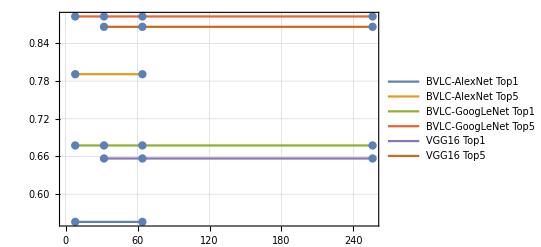

```mathematica
ListLinePlot[
Catenate[
KeyValueMap[
Function[{key,val},
{
Legended[Table[{e["BatchSize"],e["Top1"]},{e,val}],key <>" Top1"],
Legended[Table[{e["BatchSize"],e["Top5"]},{e,val}],key <>" Top5"]
}
],
models
]],
Mesh->All,
PlotTheme->"Detailed"
]
```

### Top1 / Top5 Model Accuracy on Minsky for Caffe2

```mathematica
models=GroupBy[$AccuracyInformation,Lookup["Model"]];
```

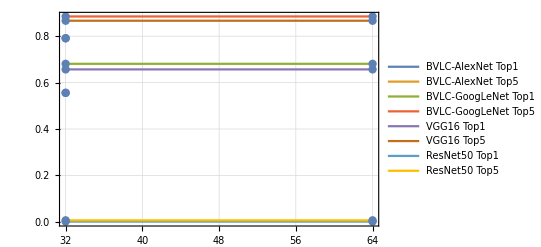

```mathematica
ListPlot[
Catenate[
KeyValueMap[
Function[{key,val},
{
Legended[Table[{e["BatchSize"],e["Top1"]},{e,val}],key <>" Top1"],
Legended[Table[{e["BatchSize"],e["Top5"]},{e,val}],key <>" Top5"]
}
],
models
]],
Joined->True,
Mesh->All,
PlotTheme->"Detailed"
]
```

```mathematica
BarChart[
Catenate[
KeyValueMap[
Function[{key,val},
Join[
Table[<|ToString[e["BatchSize"]] <> " Top1"->Callout[e["Top1"],key <> " Top1"]|>,{e,val}],
Table[<|ToString[e["BatchSize"]] <> " Top5"->Callout[e["Top5"],key <> " Top5"]|>,{e,val}]
]
],
models
]],
ChartLabels->{32,64},
ChartLegends->Automatic,
PlotTheme->"Detailed"
]
```

-Graphics-

```mathematica
Dataset[models]
```

Dataset[<>]